# Superoperators and Liouville Space

Malcolm Levitt & Christian Bengs 01-July-2023
This documentation applies to SpinDynamica v3.10

Parts 1-3 of this documentation should be read first.

SpinDynamica provides routines for defining and manipulating superoperators and their matrix representations in Liouville space, using predefined operator bases, or user-defined operator bases.

## Setup

The code in this notebook requires the installation and initialization of SpinDynamica, as described in part 1 of the documentation

```mathematica
Needs["SpinDynamica`"];
SetSpinSystem[1];
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

## Liouville space

SpinDynamica allows calculations in a space of orthogonal spin operators, known as Liouville space.

### LiouvilleBracket

In Liouville space, the scalar product of two operators is known as the Liouville bracket, and is calculated as follows: (A|B) = Tr{A^†B}, where Tr is the trace, and A^† is the adjoint of A.

In SpinDynamica the Liouville bracket of two operators is calculated using LiouvilleBracket

```mathematica
LiouvilleBracket[opI["z"],opI["x"]]
```

0

```mathematica
LiouvilleBracket[opI["z"],opI["z"]]
```

1/2

Two operators are said to be orthogonal if their Liouville bracket is zero.

#### Liouville bracket for different numbers of spins

In general, the magnitude of the Liouville bracket depends on the dimension of the state space, and hence on the number of spins.

```mathematica
SetSpinSystem[1];
LiouvilleBracket[opI["z"],opI["z"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

1/2

```mathematica
SetSpinSystem[2];
LiouvilleBracket[opI["z"],opI["z"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

2

```mathematica
SetSpinSystem[3];
LiouvilleBracket[opI["z"],opI["z"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

6

### OperatorNorm

The norm of an operator is the square root of its Liouville bracket with itself:

```mathematica
SetSpinSystem[1];
OperatorNorm[opI["z"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

1/(√2)

### NormalizeOperator

NormalizeOperator multiplies an operator by a number, so that its norm becomes 1:

```mathematica
SetSpinSystem[1];
op=NormalizeOperator[opI["z"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

√2 I_(1z)

```mathematica
OperatorNorm[op]
```

1

## operator bases

SpinDynamica includes a variety of preprogrammed operator bases. These bases are always orthonormal, meaning that each operator is normalized, and the Liouville bracket of any operator with any other is zero.

### ZeemanKetBraOperatorBasis

This is a basis formed from all ket-bra products of the Zeeman states. Consider, for example, a 2-spin-1/2 system:

```mathematica
SetSpinSystem[2]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

```mathematica
SetOperatorBasis[ZeemanKetBraOperatorBasis[]]
```

SetOperatorBasis::set: the operator basis has been set to ZeemanKetBraOperatorBasis[{{1,1/2},{2,1/2}},Sorted→Canonical].

```mathematica
BasisOperators[]
```

{|αα⟩.<αα|,|αα⟩.<βα|,|αα⟩.<αβ|,|αα⟩.<ββ|,|βα⟩.<αα|,|βα⟩.<βα|,|βα⟩.<αβ|,|βα⟩.<ββ|,|αβ⟩.<αα|,|αβ⟩.<βα|,|αβ⟩.<αβ|,|αβ⟩.<ββ|,|ββ⟩.<αα|,|ββ⟩.<βα|,|ββ⟩.<αβ|,|ββ⟩.<ββ|}

This basis is sorted in default “canonical” order, meaning that the first ket in the Zeeman basis is combined with all bras, then the second ket is combined with all bras, and so on, until all ket.bra combinations have been generated.

#### OperatorBasisDimension

The number of operators in the basis is given by OperatorBasisDimension[opbasis]. If opbasis is omitted, the current operator basis is used:

```mathematica
OperatorBasisDimension[]
```

16

#### general spin systems

The ZeemanKetBraOperatorBasis is defined for any spin system. For example, consider a spin-3/2 coupled to a spin-1:

```mathematica
SetSpinSystem[{{1,3/2},{2,1}}]
```

SetSpinSystem::set: the spin system has been set to {{1,3/2},{2,1}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,3/2},{2,1}},BasisLabels→Automatic].

```mathematica
SetOperatorBasis[ZeemanKetBraOperatorBasis[]]
```

SetOperatorBasis::set: the operator basis has been set to ZeemanKetBraOperatorBasis[{{1,3/2},{2,1}},Sorted→Canonical].

In this case, there are 144 operators in the basis:

```mathematica
OperatorBasisDimension[]
```

144

The instruction below displays the first 5 basis operators:

```mathematica
BasisOperators[]⟦Range[1,5]⟧
```

{|3/2+3/2,1+1⟩.(<3/2+3/2,1+1|),|3/2+3/2,1+1⟩.(<3/2+1/2,1+1|),|3/2+3/2,1+1⟩.(<3/2-1/2,1+1|),|3/2+3/2,1+1⟩.(<3/2-3/2,1+1|),|3/2+3/2,1+1⟩.(<3/2+3/2,10|)}

#### alternative ordering

SpinDynamica supports alternative sorting orders; for example

```mathematica
SetSpinSystem[2];SetOperatorBasis[ZeemanKetBraOperatorBasis[Sorted->"OrderBySpin"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

SetOperatorBasis::set: the operator basis has been set to ZeemanKetBraOperatorBasis[{{1,1/2},{2,1/2}},Sorted→OrderBySpin].

```mathematica
BasisOperators[]
```

{|αα⟩.<αα|,|αα⟩.<βα|,|βα⟩.<αα|,|βα⟩.<βα|,|αα⟩.<αβ|,|αα⟩.<ββ|,|βα⟩.<αβ|,|βα⟩.<ββ|,|αβ⟩.<αα|,|αβ⟩.<βα|,|ββ⟩.<αα|,|ββ⟩.<βα|,|αβ⟩.<αβ|,|αβ⟩.<ββ|,|ββ⟩.<αβ|,|ββ⟩.<ββ|}

In this case, the basis is ordered so that the states of the individual spins take precedence.

Operator bases may also be sorted according to coherence order:

```mathematica
SetOperatorBasis[ZeemanKetBraOperatorBasis[Sorted->CoherenceOrder]]
```

SetOperatorBasis::set: the operator basis has been set to ZeemanKetBraOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

```mathematica
BasisOperators[]
```

{|ββ⟩.<αα|,|ββ⟩.<βα|,|ββ⟩.<αβ|,|βα⟩.<αα|,|αβ⟩.<αα|,|ββ⟩.<ββ|,|βα⟩.<βα|,|βα⟩.<αβ|,|αβ⟩.<βα|,|αβ⟩.<αβ|,|αα⟩.<αα|,|βα⟩.<ββ|,|αβ⟩.<ββ|,|αα⟩.<βα|,|αα⟩.<αβ|,|αα⟩.<ββ|}

The sequence of coherence orders is revealed by mapping CoherenceOrder onto each basis operator:

```mathematica
CoherenceOrder/@BasisOperators[]
```

{-2,-1,-1,-1,-1,0,0,0,0,0,0,1,1,1,1,2}

### ShiftAndZOperatorBasis

This is a basis consisting of products of z-operators and shift operators. In this case, the default ordering is to sort the operators according to their coherence order.

Consider a 2-spin-1/2 system again:

```mathematica
SetSpinSystem[2];
SetOperatorBasis[ShiftAndZOperatorBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

```mathematica
BasisOperators[]
```

{I_1^-•I_2^-,√2 (I_1^-•I_(2z)),√2 (I_(1z)•I_2^-),I_1^-/(√2),I_2^-/(√2),I_1^-•I_2^+,I_1^+•I_2^-,2 (I_(1z)•I_(2z)),I_(1z),I_(2z),𝟙/2,√2 (I_1^+•I_(2z)),√2 (I_(1z)•I_2^+),I_1^+/(√2),I_2^+/(√2),I_1^+•I_2^+}

all operators in the basis are orthogonal and normalized, for example:

```mathematica
op1=BasisOperators[]⟦5⟧
op2=BasisOperators[]⟦8⟧
```

I_2^-/(√2)

2 (I_(1z)•I_(2z))

```mathematica
LiouvilleBracket[op1,op1]
LiouvilleBracket[op1,op2]
LiouvilleBracket[op2,op2]
```

1

0

1

By default, the operators in this basis are sorted in ascending coherence order:

```mathematica
CoherenceOrder/@BasisOperators[]
```

{-2,-1,-1,-1,-1,0,0,0,0,0,0,1,1,1,1,2}

#### general spin systems

ShiftAndZOperatorBasis is defined for any spin system. For example:

```mathematica
SetSpinSystem[{{1,3/2},{2,1/2}}];
SetOperatorBasis[ShiftAndZOperatorBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,3/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,3/2},{2,1/2}},BasisLabels→Automatic].

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,3/2},{2,1/2}},Sorted→CoherenceOrder].

Here are some of the basis operators in this case:

```mathematica
BasisOperators[]⟦Range[10,15]⟧
```

{(I_1^-•I_(1z)•I_2^-+I_(1z)•I_1^-•I_2^-)/(2 √6),1/6 (I_1^-•I_1^-•I_1^-•I_2^+),(I_1^-•I_1^-•I_(1z)•I_(2z)+I_(1z)•I_1^-•I_1^-•I_(2z))/(2 √3),(-17 (I_1^-•I_2^-)+10 (I_1^-•I_(1z)•I_(1z)•I_2^-+I_(1z)•I_(1z)•I_1^-•I_2^-))/(8 √15),(I_1^-•I_(2z))/(√5),(I_1^-•I_(1z)+I_(1z)•I_1^-)/(4 √3)}

Note that the orthonormal combinations of z and shift operators are not intuitive for spins > 1/2

#### alternative ordering

SpinDynamica supports alternative sorting orders; for example

```mathematica
SetSpinSystem[2];
SetOperatorBasis[ShiftAndZOperatorBasis[Sorted->"OrderBySpin"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2}},Sorted→OrderBySpin].

In this case, all possible operators for spin #1 are multiplied by the first operator for spin #2, followed by all possible operators for spin #1 multiplied by the second operator for spin #2, and so on, until all combinations are generated.

```mathematica
BasisOperators[]
```

{I_1^-•I_2^-,I_2^-/(√2),√2 (I_(1z)•I_2^-),I_1^+•I_2^-,I_1^-/(√2),𝟙/2,I_(1z),I_1^+/(√2),√2 (I_1^-•I_(2z)),I_(2z),2 (I_(1z)•I_(2z)),√2 (I_1^+•I_(2z)),I_1^-•I_2^+,I_2^+/(√2),√2 (I_(1z)•I_2^+),I_1^+•I_2^+}

This basis does not have a regular set of coherence orders:

```mathematica
CoherenceOrder/@BasisOperators[]
```

{-2,-1,-1,0,-1,0,0,1,-1,0,0,1,0,1,1,2}

### CartesianProductOperatorBasis

This is a basis consisting of products of angular momentum operators along the x, y or z axes. In this case, the default ordering is to sort the operators according to their SpinProductRank, i.e. the number of angular momentum operators in the product

Consider a 2-spin-1/2 system again:

```mathematica
SetSpinSystem[2];
SetOperatorBasis[CartesianProductOperatorBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetOperatorBasis::set: the operator basis has been set to CartesianProductOperatorBasis[{{1,1/2},{2,1/2}},Sorted→SpinProductRank].

```mathematica
BasisOperators[]
```

{𝟙/2,I_(1x),I_(1y),I_(1z),I_(2x),I_(2y),I_(2z),2 (I_(1x)•I_(2x)),2 (I_(1x)•I_(2y)),2 (I_(1x)•I_(2z)),2 (I_(1y)•I_(2x)),2 (I_(1y)•I_(2y)),2 (I_(1y)•I_(2z)),2 (I_(1z)•I_(2x)),2 (I_(1z)•I_(2y)),2 (I_(1z)•I_(2z))}

The spin product rank of each basis operator is revealed as follows:

```mathematica
SpinProductRank/@BasisOperators[]
```

{0,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2}

#### alternative ordering

SpinDynamica supports alternative sorting orders; for example

```mathematica
SetSpinSystem[2];SetOperatorBasis[CartesianProductOperatorBasis[Sorted->"OrderBySpin"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetOperatorBasis::set: the operator basis has been set to CartesianProductOperatorBasis[{{1,1/2},{2,1/2}},Sorted→OrderBySpin].

In this case, all possible operators for spin #1 are multiplied by the first operator for spin #2, followed by all possible operators for spin #1 multiplied by the second operator for spin #2, and so on, until all combinations are generated.

```mathematica
BasisOperators[]
```

{𝟙/2,I_(1x),I_(1y),I_(1z),I_(2x),2 (I_(1x)•I_(2x)),2 (I_(1y)•I_(2x)),2 (I_(1z)•I_(2x)),I_(2y),2 (I_(1x)•I_(2y)),2 (I_(1y)•I_(2y)),2 (I_(1z)•I_(2y)),I_(2z),2 (I_(1x)•I_(2z)),2 (I_(1y)•I_(2z)),2 (I_(1z)•I_(2z))}

This basis does not have a regular set of spin product ranks:

```mathematica
SpinProductRank/@BasisOperators[]
```

{0,1,1,1,1,2,2,2,1,2,2,2,1,2,2,2}

#### general spin systems

CartesianProductOperatorBasis is also defined for systems of spins > 1/2. However the combinations of operators leading to an orthogonal basis is not intuitive in this case. The example below is for a single spin-3/2:

```mathematica
SetSpinSystem[{{1,3/2}}];
SetOperatorBasis[CartesianProductOperatorBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,3/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,3/2}},BasisLabels→Automatic].

SetOperatorBasis::set: the operator basis has been set to CartesianProductOperatorBasis[{{1,3/2}},Sorted→SpinProductRank].

```mathematica
BasisOperators[]
```

{𝟙/2,(I_(1x))/(√5),(I_(1y))/(√5),(I_(1z))/(√5),(10 (I_(1x)•I_(1z)•I_(1z))+10 (I_(1z)•I_(1z)•I_(1x))-17 I_(1x))/(4 √30),(10 (I_(1y)•I_(1z)•I_(1z))+10 (I_(1z)•I_(1z)•I_(1y))-17 I_(1y))/(4 √30),(20 (I_(1z)•I_(1z)•I_(1z))-41 I_(1z))/(12 √5),1/8 (4 (I_(1z)•I_(1z))-5 𝟙),(I_(1x)•I_(1y)+I_(1y)•I_(1x))/(2 √3),(I_(1x)•I_(1x)-I_(1y)•I_(1y))/(2 √3),(I_(1x)•I_(1z)+I_(1z)•I_(1x))/(2 √3),(I_(1y)•I_(1z)+I_(1z)•I_(1y))/(2 √3),(I_(1x)•I_(1x)•I_(1x)-I_(1x)•I_(1y)•I_(1y)-I_(1y)•I_(1x)•I_(1y)-I_(1y)•I_(1y)•I_(1x))/(3 √2),(I_(1x)•I_(1x)•I_(1y)+I_(1x)•I_(1y)•I_(1x)+I_(1y)•I_(1x)•I_(1x)-I_(1y)•I_(1y)•I_(1y))/(3 √2),(I_(1x)•I_(1y)•I_(1z)+I_(1y)•I_(1x)•I_(1z)+I_(1z)•I_(1x)•I_(1y)+I_(1z)•I_(1y)•I_(1x))/(2 √3),(I_(1x)•I_(1x)•I_(1z)-I_(1y)•I_(1y)•I_(1z)+I_(1z)•I_(1x)•I_(1x)-I_(1z)•I_(1y)•I_(1y))/(2 √3)}

### ShiftAndPolarizationOperatorBasis

This is a basis consisting of products of the I^+, I^-, I^α and I^β operators. This basis is only available for spins-1/2.

```mathematica
SetSpinSystem[2];
SetOperatorBasis[ShiftAndPolarizationOperatorBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

SetOperatorBasis::set: the operator basis has been set to ShiftAndPolarizationOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

```mathematica
BasisOperators[]
```

{I_1^-•I_2^-,I_1^-•I_2^α,I_1^-•I_2^β,I_1^α•I_2^-,I_1^β•I_2^-,I_1^-•I_2^+,I_1^+•I_2^-,I_1^α•I_2^α,I_1^α•I_2^β,I_1^β•I_2^α,I_1^β•I_2^β,I_1^+•I_2^α,I_1^+•I_2^β,I_1^α•I_2^+,I_1^β•I_2^+,I_1^+•I_2^+}

### SingletTripletOperatorBasis

In the special case of a 2-spin-1/2 system, two different versions of a SingletTripletOperatorBasis are available:

```mathematica
SetSpinSystem[2];
SetOperatorBasis[SingletTripletOperatorBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetOperatorBasis::set: the operator basis has been set to SingletTripletOperatorBasis[1,{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

```mathematica
BasisOperators[]
```

{|ββ⟩.<αα|,(|βα⟩.<αα|+|αβ⟩.<αα|)/(√2),(-|βα⟩.<αα|+|αβ⟩.<αα|)/(√2),(|ββ⟩.<βα|+|ββ⟩.<αβ|)/(√2),(-|ββ⟩.<βα|+|ββ⟩.<αβ|)/(√2),1/2 (-|βα⟩.<βα|+|βα⟩.<αβ|-|αβ⟩.<βα|+|αβ⟩.<αβ|),1/2 (-|βα⟩.<βα|-|βα⟩.<αβ|+|αβ⟩.<βα|+|αβ⟩.<αβ|),|ββ⟩.<ββ|,1/2 (|βα⟩.<βα|+|βα⟩.<αβ|+|αβ⟩.<βα|+|αβ⟩.<αβ|),|αα⟩.<αα|,1/2 (|βα⟩.<βα|-|βα⟩.<αβ|-|αβ⟩.<βα|+|αβ⟩.<αβ|),(|βα⟩.<ββ|+|αβ⟩.<ββ|)/(√2),(-|βα⟩.<ββ|+|αβ⟩.<ββ|)/(√2),(|αα⟩.<βα|+|αα⟩.<αβ|)/(√2),(-|αα⟩.<βα|+|αα⟩.<αβ|)/(√2),|αα⟩.<ββ|}

```mathematica
SetOperatorBasis[SingletTripletOperatorBasis[2]]
```

SetOperatorBasis::set: the operator basis has been set to SingletTripletOperatorBasis[2,{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

```mathematica
BasisOperators[]
```

{|ββ⟩.<αα|,(-|ββ⟩.<βα|+|ββ⟩.<αβ|)/(√2),(|ββ⟩.<βα|+|ββ⟩.<αβ|)/(√2),(-|βα⟩.<αα|+|αβ⟩.<αα|)/(√2),(|βα⟩.<αα|+|αβ⟩.<αα|)/(√2),1/2 (-|βα⟩.<βα|+|βα⟩.<αβ|-|αβ⟩.<βα|+|αβ⟩.<αβ|),1/2 (-|βα⟩.<βα|-|βα⟩.<αβ|+|αβ⟩.<βα|+|αβ⟩.<αβ|),(-|ββ⟩.<ββ|+|βα⟩.<βα|+|βα⟩.<αβ|+|αβ⟩.<βα|+|αβ⟩.<αβ|-|αα⟩.<αα|)/(√6),(-|ββ⟩.<ββ|+|αα⟩.<αα|)/(√2),-(|ββ⟩.<ββ|-|βα⟩.<βα|+2 |βα⟩.<αβ|+2 |αβ⟩.<βα|-|αβ⟩.<αβ|+|αα⟩.<αα|)/(2 √3),1/2 (|ββ⟩.<ββ|+|βα⟩.<βα|+|αβ⟩.<αβ|+|αα⟩.<αα|),(-|βα⟩.<ββ|+|αβ⟩.<ββ|)/(√2),(|βα⟩.<ββ|+|αβ⟩.<ββ|)/(√2),(-|αα⟩.<βα|+|αα⟩.<αβ|)/(√2),(|αα⟩.<βα|+|αα⟩.<αβ|)/(√2),|αα⟩.<ββ|}

### SphericalTensorOperatorBasis

Normalized bases of spherical tensor operators are available for any spin system:

```mathematica
SetSpinSystem[2];
SetOperatorBasis[SphericalTensorOperatorBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetOperatorBasis::set: the operator basis has been set to SphericalTensorOperatorBasis[{{1,1/2},{2,1/2}},Sorted→{CoherenceOrder,SphericalRank}].

```mathematica
BasisOperators[]
```

{I_1^-•I_2^-,I_2^-/(√2),I_1^-/(√2),-(I_1^-•I_(2z))+I_(1z)•I_2^-,I_1^-•I_(2z)+I_(1z)•I_2^-,𝟙/2,-(I_1^-•I_2^++I_1^+•I_2^-+2 (I_(1z)•I_(2z)))/(√3),I_(2z),I_(1z),(I_1^-•I_2^+-I_1^+•I_2^-)/(√2),-(I_1^-•I_2^++I_1^+•I_2^--4 (I_(1z)•I_(2z)))/(√6),-I_2^+/(√2),-I_1^+/(√2),-(I_1^+•I_(2z))+I_(1z)•I_2^+,-(I_1^+•I_(2z))-I_(1z)•I_2^+,I_1^+•I_2^+}

The {rank,component} values of the basis operators may be obtained by applying SphericalTensorIndices to the basis:

```mathematica
SphericalTensorIndices[SphericalTensorOperatorBasis[]]
```

{{2,-2},{1,-1},{1,-1},{1,-1},{2,-1},{0,0},{0,0},{1,0},{1,0},{1,0},{2,0},{1,1},{1,1},{1,1},{2,1},{2,2}}

Note that there may be several operators with the same {rank,component} values.

The current operator basis is assumed, if it is not specified.

```mathematica
SphericalTensorIndices[]
```

{{2,-2},{1,-1},{1,-1},{1,-1},{2,-1},{0,0},{0,0},{1,0},{1,0},{1,0},{2,0},{1,1},{1,1},{1,1},{2,1},{2,2}}

### user-defined operator bases

Any orthonormal set of operators may be defined by the user as an operator basis. For example, the following instructions take the basis operators for spin #1 in a ShiftAndZOperatorBasis, and multiply them by all basis operators for spin #2 in a CartesianProductOperatorBasis. This set of operators is used to construct a user-defined operator basis for Liouville space:

```mathematica
SetSpinSystem[2];ops1=BasisOperators[ShiftAndZOperatorBasis[{{1,1/2}}]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

{I_1^-,√2 I_(1z),𝟙/(√2),I_1^+}

```mathematica
ops2=BasisOperators[CartesianProductOperatorBasis[{{2,1/2}}]]
```

{𝟙/(√2),√2 I_(2x),√2 I_(2y),√2 I_(2z)}

```mathematica
newbasisops=Flatten@Outer[Dot,ops1,ops2]
```

{I_1^-/(√2),√2 (I_1^-•I_(2x)),√2 (I_1^-•I_(2y)),√2 (I_1^-•I_(2z)),I_(1z),2 (I_(1z)•I_(2x)),2 (I_(1z)•I_(2y)),2 (I_(1z)•I_(2z)),𝟙/2,I_(2x),I_(2y),I_(2z),I_1^+/(√2),√2 (I_1^+•I_(2x)),√2 (I_1^+•I_(2y)),√2 (I_1^+•I_(2z))}

```mathematica
DefineOperatorBasis[newopbasis,newbasisops]
```

DefineOperatorBasis::maybeslow: An OperatorBasis consisting of an arbitrary set of operators may be slow to set up for larger spin systems. Consider using one of the special cases of DefineOperatorBasis (execute ?DefineOperatorBasis for details).

CheckOperatorBasis::orthonormal: Operator basis is orthonormal.

DefineOperatorBasis::defined: The operator basis newopbasis has been defined.

newopbasis

The DefineOperatorBasis routine automatically checks for appropriate properties.

To use this basis, SetOperatorBasis is needed:

```mathematica
SetSpinSystem[2];
SetOperatorBasis[newopbasis]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetOperatorBasis::set: the operator basis has been set to newopbasis.

CheckOperatorBasis::orthonormal: Operator basis is orthonormal.

```mathematica
BasisOperators[]
```

{I_1^-/(√2),√2 (I_1^-•I_(2x)),√2 (I_1^-•I_(2y)),√2 (I_1^-•I_(2z)),I_(1z),2 (I_(1z)•I_(2x)),2 (I_(1z)•I_(2y)),2 (I_(1z)•I_(2z)),𝟙/2,I_(2x),I_(2y),I_(2z),I_1^+/(√2),√2 (I_1^+•I_(2x)),√2 (I_1^+•I_(2y)),√2 (I_1^+•I_(2z))}

## general operator basis routines

### OperatorBasisDimension

OperatorBasisDimension[opbasis] returns the number of operators in an operator basis:

```mathematica
OperatorBasisDimension[ZeemanKetBraOperatorBasis[5]]
```

1024

### ExpressOperator

ExpressOperator[op, opbasis] expresses any operator op as a combination of basis operators for the operator basis opbasis. If opbasis is omitted, the current operator basis is used.

The instructions below express a rank-3 spherical tensor operator for 3-spins-1/2 as a combination of Cartesian product operators.

```mathematica
SetSpinSystem[3];
SetOperatorBasis[CartesianProductOperatorBasis[]];
ExpressOperator[opT[{1,2,3},{3,3}]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

SetOperatorBasis::set: the operator basis has been set to CartesianProductOperatorBasis[{{1,1/2},{2,1/2},{3,1/2}},Sorted→SpinProductRank].

-(I_(1x)•I_(2x)•I_(3x))/(2 √2)-(ⅈ (I_(1x)•I_(2x)•I_(3y)))/(2 √2)-(ⅈ (I_(1x)•I_(2y)•I_(3x)))/(2 √2)+(I_(1x)•I_(2y)•I_(3y))/(2 √2)-(ⅈ (I_(1y)•I_(2x)•I_(3x)))/(2 √2)+(I_(1y)•I_(2x)•I_(3y))/(2 √2)+(I_(1y)•I_(2y)•I_(3x))/(2 √2)+(ⅈ (I_(1y)•I_(2y)•I_(3y)))/(2 √2)

These instructions express a rotation operator in terms of Cartesian product operators:

```mathematica
ExpressOperator[opR[{β,"x"}]]
```

-2 ⅈ Cos[β/2]^2 I_(1x) Sin[β/2]-2 ⅈ Cos[β/2]^2 I_(2x) Sin[β/2]-2 ⅈ Cos[β/2]^2 I_(3x) Sin[β/2]-4 Cos[β/2] (I_(1x)•I_(2x)) Sin[β/2]^2-4 Cos[β/2] (I_(1x)•I_(3x)) Sin[β/2]^2-4 Cos[β/2] (I_(2x)•I_(3x)) Sin[β/2]^2+8 ⅈ (I_(1x)•I_(2x)•I_(3x)) Sin[β/2]^3+Cos[β/2]^3 𝟙

### OperatorBasisTransformationMatrix

OperatorBasisTransformationMatrix[opbasis2,opbasis1] provides the matrix which transforms the set of basis operators for opbasis1 into those for opbasis2.

This code displays the transformation matrix from the ZeemanKetBraOperatorBasis to the CartesianProductOperatorBasis, for a 2-spin-1/2 system:

```mathematica
SetSpinSystem[2];
OperatorBasisTransformationMatrix[CartesianProductOperatorBasis[],ZeemanKetBraOperatorBasis[]]//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

(1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2
0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0
0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0
1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0
0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2
0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | -1/2 | 0
0 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0 | -ⅈ/2 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/2 | 0 | 0 | ⅈ/2 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0
0 | 0 | ⅈ/2 | 0 | 0 | 0 | 0 | -ⅈ/2 | -ⅈ/2 | 0 | 0 | 0 | 0 | ⅈ/2 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2)

## Superoperators

Superoperators generate a linear transformation of an operator into another operator. SpinDynamica supports a set of common superoperator types.

The matrix representation of a superoperator in a particular operator basis is generated using SuperoperatorMatrixRepresentation. Examples are given below.

### CommutationSuperoperator

The CommutationSuperoperator of any operator is defined through CommutationSuperoperator[op]. When this superoperator is applied to another operator, the commutator is generated, for example:

```mathematica
SetSpinSystem[1];CommutationSuperoperator[opI["x"]][opI["y"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

I_(1x)•I_(1y)-I_(1y)•I_(1x)

or

```mathematica
csop=CommutationSuperoperator[opI["x"]];
csop[opI["y"]]
```

I_(1x)•I_(1y)-I_(1y)•I_(1x)

The matrix representation of a superoperator in a particular operator basis is generated using SuperoperatorMatrixRepresentation, for example:

```mathematica
SetSpinSystem[1];
SetOperatorBasis[CartesianProductOperatorBasis[]];
SuperoperatorMatrixRepresentation[CommutationSuperoperator[opI["x"]]]//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetOperatorBasis::set: the operator basis has been set to CartesianProductOperatorBasis[{{1,1/2}},Sorted→SpinProductRank].

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0)

### DoubleCommutationSuperoperator

A DoubleCommutationSuperoperator generates two successive commutators, involving two different operators, for example

```mathematica
dcomsop=DoubleCommutationSuperoperator[opI["x"],opI["y"]]
```

DoubleCommutationSuperoperator[I_(1x),I_(1y)]

leading to

```mathematica
dcomsop[opI["z"]]
```

I_(1x)•I_(1y)•I_(1z)-I_(1x)•I_(1z)•I_(1y)-I_(1y)•I_(1z)•I_(1x)+I_(1z)•I_(1y)•I_(1x)

DoubleCommutationSuperoperators are often used for representing relaxation processes.

SuperoperatorMatrixRepresentation may be used to generate the matrix representation in any operator basis:

```mathematica
SetSpinSystem[1];
SetOperatorBasis[CartesianProductOperatorBasis[]];
SuperoperatorMatrixRepresentation[DoubleCommutationSuperoperator[opI["x"],opI["y"]]]//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetOperatorBasis::alreadyset: The operator basis is already set to CartesianProductOperatorBasis[{{1,1/2}},Sorted→SpinProductRank]. No action has been taken.

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 0 | 0)

### Lindbladian

The Lindbladian symbol generates a Lindbladian dissipation superoperator, as described in Bengs and Levitt, doi.org/10.1016/j.jmr.2019.106645. The Lindbladian dissipator D̂(A,B) depends on two operators, A and B, and when acting on an operator C, generates the following expression: D̂(A,B) (C) = ACB-1/2(BAC+CBA). Lindbladian superoperators provide a rigorous means to treat spin dynamics in the presence of relaxation through contact with an environment at finite temperature. See the relaxation part of  the documentation for examples.

```mathematica
LBsop=Lindbladian[opI["+"],opI["-"]]
```

Lindbladian[I_1^+,I_1^-]

leading to

```mathematica
LBsop[opI["z"]]
```

-I_(1z)

SuperoperatorMatrixRepresentation may be used to generate the matrix representation in any operator basis:

```mathematica
SetSpinSystem[1];
SetOperatorBasis[CartesianProductOperatorBasis[]];
SuperoperatorMatrixRepresentation[Lindbladian[opI["+"],opI["-"]]]//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetOperatorBasis::alreadyset: The operator basis is already set to CartesianProductOperatorBasis[{{1,1/2}},Sorted→SpinProductRank]. No action has been taken.

(0 | 0 | 0 | 0
0 | -1/2 | 0 | 0
0 | 0 | -1/2 | 0
1 | 0 | 0 | -1)

### LeftMultiplicationSuperoperator and RightMultiplicationSuperoperator

Left and RightMultiplicationSuperoperators may be defined through the use of LeftMultiplicationSuperoperator[op] and RightMultiplicationSuperoperator[op]. 

Left and RightMultplicationSuperoperators multiply their operator argument from the left and right, respectively.

```mathematica
SetSpinSystem[1];
LeftMultiplicationSuperoperator[opI["x"]][opI["y"]]
RightMultiplicationSuperoperator[opI["x"]][opI["y"]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

I_(1x)•I_(1y)

I_(1y)•I_(1x)

The difference of the same Left and RightMultplicationSuperoperator generates the corresponding CommutationSuperoperator.

```mathematica
LeftMultiplicationSuperoperator[opI["x"]][opI["y"]]-RightMultiplicationSuperoperator[opI["x"]][opI["y"]]
```

I_(1x)•I_(1y)-I_(1y)•I_(1x)

SuperoperatorMatrixRepresentation may be used to generate the corresponding representations with respect to a particular basis.

```mathematica
SetSpinSystem[1];
SetOperatorBasis[CartesianProductOperatorBasis[]];
SuperoperatorMatrixRepresentation[LeftMultiplicationSuperoperator[opI["x"]]]//MatrixForm
SuperoperatorMatrixRepresentation[RightMultiplicationSuperoperator[opI["x"]]]//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetOperatorBasis::alreadyset: The operator basis is already set to CartesianProductOperatorBasis[{{1,1/2}},Sorted→SpinProductRank]. No action has been taken.

(0 | 1/2 | 0 | 0
1/2 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2
0 | 0 | ⅈ/2 | 0)

(0 | 1/2 | 0 | 0
1/2 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/2
0 | 0 | -ⅈ/2 | 0)

### RotationSuperoperator

RotationSuperoperators have been defined in part 1 of this documentation. They may be used to represent instantaneous rotations of one or more spins, as induced by an ideal, infinitely short, radiofrequency pulse.

When a RotationSuperoperator is applied to an operator, it sandwiches the operator between two opposite rotation operators:

```mathematica
RotationSuperoperator[{π/2,"x"}][opI["y"]]
```

R_(1x)(π/2)•I_(1y)•R_(1x)(-π/2)

SuperoperatorMatrixRepresentation may be used to generate the matrix representation in any operator basis:

```mathematica
SetSpinSystem[1];
SetOperatorBasis[CartesianProductOperatorBasis[]];
SuperoperatorMatrixRepresentation[RotationSuperoperator[{β,"x"}]]//Normal//Simplify//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetOperatorBasis::alreadyset: The operator basis is already set to CartesianProductOperatorBasis[{{1,1/2}},Sorted→SpinProductRank]. No action has been taken.

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | Cos[β] | -Sin[β]
0 | 0 | Sin[β] | Cos[β])

### CoherenceOrderFiltrationSuperoperator

CoherenceOrderFiltrationSuperoperator was defined in part 1 of this documentation.

When CoherenceOrderFiltrationSuperoperator is applied to an operator, it projects out the part which has the specified coherence order:

```mathematica
CoherenceOrderFiltrationSuperoperator[1][opI["y"]]//Simplify
```

1/2 (-ⅈ I_(1x)+I_(1y))

```mathematica
CoherenceOrder[%]
```

1

A set of coherence orders, and a set of relevant spins, may be specified. The instruction below filters out the operators which have order 0 or 2, for spins #1 and #2:

```mathematica
SetSpinSystem[4];
CoherenceOrderFiltrationSuperoperator[{1,2},{2,0}][opI[1,"y"].opI[2,"x"].opI[3,"z"]]//Simplify
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2},{4,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2},{4,1/2}},BasisLabels→Automatic].

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2},{3,1/2},{4,1/2}},Sorted→CoherenceOrder].

1/4 ⅈ (I_1^-•I_2^+•I_(3z)-I_1^+•I_2^-•I_(3z)-I_1^+•I_2^+•I_(3z))

Successive coherence order filtrations may be specified by using 2 or more arguments for CoherenceOrderFiltrationSuperoperator. In the example below, terms which are zero-quantum for both sets of spins {1,2} and {3,4} are extracted:

```mathematica
SetSpinSystem[4];
CoherenceOrderFiltrationSuperoperator[{{1,2},0},{{3,4},0}][opI[1,"y"].opI[2,"x"].opI[3,"x"].opI[4,"y"]]//Simplify
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2},{4,1/2}}

1/16 (I_1^-•I_2^+•I_3^-•I_4^+-I_1^-•I_2^+•I_3^+•I_4^--I_1^+•I_2^-•I_3^-•I_4^++I_1^+•I_2^-•I_3^+•I_4^-)

The result is more selective than when terms which are zero-quantum for any combination of spins is extracted:

```mathematica
SetSpinSystem[4];
CoherenceOrderFiltrationSuperoperator[0][opI[1,"y"].opI[2,"x"].opI[3,"x"].opI[4,"y"]]//Simplify
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2},{4,1/2}}

1/16 (I_1^-•I_2^-•I_3^+•I_4^++I_1^-•I_2^+•I_3^-•I_4^+-I_1^-•I_2^+•I_3^+•I_4^--I_1^+•I_2^-•I_3^-•I_4^++I_1^+•I_2^-•I_3^+•I_4^-+I_1^+•I_2^+•I_3^-•I_4^-)

SuperoperatorMatrixRepresentation may be used to generate the matrix representation in any operator basis:

```mathematica
SetSpinSystem[1];
SetOperatorBasis[CartesianProductOperatorBasis[]];
SuperoperatorMatrixRepresentation[CoherenceOrderFiltrationSuperoperator[1]
]//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

SetOperatorBasis::set: the operator basis has been set to CartesianProductOperatorBasis[{{1,1/2}},Sorted→SpinProductRank].

(0 | 0 | 0 | 0
0 | 1/2 | -ⅈ/2 | 0
0 | ⅈ/2 | 1/2 | 0
0 | 0 | 0 | 0)

### SpinPermutationSuperoperator

SpinPermutationSuperoperator is the superoperator for a permutation of spins. The general syntax is SpinPermutationSuperoperator[{j,k,l,..m}] which indicates a cyclic permutation of spins, i.e. j→k, k→l, .., m→j.

For example, the effect of cyclically permuting the 3 spins in a product operator may be calculated as follows:

```mathematica
SetSpinSystem[3];
SetOperatorBasis[CartesianProductOperatorBasis[]]
SpinPermutationSuperoperator[{1,2,3}][4 opI[1,"x"].opI[2,"y"].opI[3,"z"]]
SpinPermutationSuperoperator[{1,2,3}][%]
SpinPermutationSuperoperator[{1,2,3}][%]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

SetOperatorBasis::set: the operator basis has been set to CartesianProductOperatorBasis[{{1,1/2},{2,1/2},{3,1/2}},Sorted→SpinProductRank].

4 (I_(1z)•I_(2x)•I_(3y))

4 (I_(1y)•I_(2z)•I_(3x))

4 (I_(1x)•I_(2y)•I_(3z))

Note that 3 cyclic permutations restores the original operator

The matrix representation of a SpinPermutationSuperoperator may be calculated in the usual way:

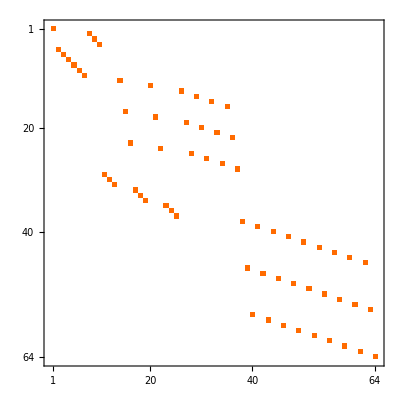

```mathematica
SuperoperatorMatrixRepresentation[SpinPermutationSuperoperator[{1,2,3}]]//MatrixPlot
```

### ProjectionSuperoperator

ProjectionSuperoperator[op] removes the parts of an operator which are orthogonal to the operator op.

For example, in a 2-spin system, the scalar product opI[1].opI[2] contains the term opI[1,”z”].opI[2,”z”] as well as orthogonal terms:

```mathematica
SetSpinSystem[2];
opI[1].opI[2]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

(I⃗)_1•(I⃗)_2

The orthogonal terms may be removed by using ProjectionSuperoperator:

```mathematica
ProjectionSuperoperator[opI[1,"z"].opI[2,"z"]][opI[1].opI[2]]
```

I_(1z)•I_(2z)

### SuperoperatorType

SuperoperatorType may be applied to a superoperator to determine whether it is Hermitian, antiHermitian, Unitary, Normal, etc.

```mathematica
SuperoperatorType[CommutationSuperoperator[opI["x"]]]
```

Hermitian

```mathematica
SuperoperatorType[-I CommutationSuperoperator[opI["x"]]]
```

AntiHermitian

```mathematica
SuperoperatorType[DoubleCommutationSuperoperator[opI["x"],opI["x"]]]
```

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

Hermitian

### exponentials of Superoperators

SpinDynamica may handle the exponents of superoperators, which are often used in spin dynamical calculations.

The lines below take the complex exponential of the superoperator for commutation under a Cartesian product operator:

```mathematica
SetSpinSystem[2];
sop = Exp[-I β CommutationSuperoperator[2 opI[1,"z"].opI[2,"z"]]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

ⅇ^CommutationSuperoperator[-2 ⅈ β (I_(1z)•I_(2z))]

The matrix representation of this superoperator is displayed as follows:

```mathematica
SetOperatorBasis[CartesianProductOperatorBasis[]];
SuperoperatorMatrixRepresentation[sop]//ExpToTrig//Simplify//MatrixForm
```

SetOperatorBasis::set: the operator basis has been set to CartesianProductOperatorBasis[{{1,1/2},{2,1/2}},Sorted→SpinProductRank].

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Cos[β] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Sin[β] | 0 | 0 | 0
0 | 0 | Cos[β] | 0 | 0 | 0 | 0 | 0 | 0 | Sin[β] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Cos[β] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Sin[β] | 0
0 | 0 | 0 | 0 | 0 | Cos[β] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[β] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Sin[β] | 0 | 0 | 0 | 0 | 0 | 0 | Cos[β] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | Sin[β] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[β] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Sin[β] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[β] | 0 | 0
0 | 0 | 0 | 0 | Sin[β] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[β] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

The trigonometric factors correspond to the Cartesian product operator calculations of spin dynamics in weakly-coupled spin systems.

### Superoperator

The routine Superoperator may be used to define a superoperator using its matrix representation in a given operator basis.

```mathematica
SetSpinSystem[1];
sop=Superoperator[{{1,0,0,0},{0,0,1,0},{0,0,0,0},{0,0,0,0}},CartesianProductOperatorBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

Superoperator[<<..>>, SuperoperatorType→None]

The matrix representation of this superoperator may now be expressed in any desired basis:

```mathematica
SuperoperatorMatrixRepresentation[sop,ZeemanKetBraOperatorBasis[]]//MatrixForm
```

(1/2 | 0 | 0 | 1/2
0 | ⅈ/2 | -ⅈ/2 | 0
0 | ⅈ/2 | -ⅈ/2 | 0
1/2 | 0 | 0 | 1/2)

```mathematica
SuperoperatorMatrixRepresentation[sop,CartesianProductOperatorBasis[]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Superoperator may also be applied to an existing superoperator in order to store its matrix representation for later reuse.

```mathematica
sop=Superoperator[CommutationSuperoperator[opI["x"]]]
```

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2}},Sorted→CoherenceOrder].

Superoperator[CommutationSuperoperator[Operator[<<{2,2}>>]], SuperoperatorType→"Hermitian"]

```mathematica
SuperoperatorMatrixRepresentation[sop,CartesianProductOperatorBasis[]]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0)

### NDiagonalize

NDiagonalize may be used to convert any superoperator into a form which is diagonalized in a specified operator basis (or in the current operator basis, by default). The output of NDiagonalize is a special form of Superoperator which may be used just like any other superoperator. Certain routines run faster when superoperators have been preconverted into a diagonalized form.

#### example

```mathematica
SetSpinSystem[2];
sop=NDiagonalize[CommutationSuperoperator[2 opI[1,"x"].opI[2,"y"]]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

Superoperator[DiagonalizedForm[<<..{16,16}..>>], SuperoperatorType→"Hermitian"]

```mathematica
SuperoperatorMatrixRepresentation[sop]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ | 0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0
0 | 0 | 0 | 0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0 | 0
0 | 0 | 0.-0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ | 0 | 0 | 0
0 | 0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.5 ⅈ | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ | 0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ
0.-0.5 ⅈ | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0.-0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0
0 | 0 | 0 | 0.-0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ | 0 | 0
0 | 0 | 0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0 | 0 | 0
0 | 0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ | 0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0)

#### output of NDiagonalize

The output of NDiagonalize, when applied to a superoperator, has the form Superoperator[{X,evals,Xinv}, opbasis, ...] where evals is the vector of eigenvalues, X is a matrix whose columns are the eigenvectors of the matrix representation of the superoperator in the operator basis opbasis, and Xinv is the inverse of X. The elements {X,evals,Xinv} may be inspected by applying First to the output of NDiagonalize.

```mathematica
{X,evals,Xinv}=First[sop]
```

{SparseArray[…],{0,0,1.,1.,0,0,1.,1.,-1.,-1.,0,0,-1.,-1.,0,0},SparseArray[…]}

```mathematica
MatrixForm[X]
evals
MatrixForm[Xinv]
```

(0 | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ | 0 | 0.-0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ | 0 | 0.-0.5 ⅈ
0 | 0.+0.353553 ⅈ | 0 | 0.-0.353553 ⅈ | 0.+0.353553 ⅈ | 0 | 0.-0.353553 ⅈ | 0 | 0 | 0.+0.353553 ⅈ | 0 | 0.-0.353553 ⅈ | 0.+0.353553 ⅈ | 0 | 0.-0.353553 ⅈ | 0
0 | -0.353553 | 0 | 0.353553 | -0.353553 | 0 | -0.353553 | 0 | 0 | 0.353553 | 0 | -0.353553 | -0.353553 | 0 | -0.353553 | 0
0 | 0.+0.353553 ⅈ | 0 | 0.-0.353553 ⅈ | 0.-0.353553 ⅈ | 0 | 0.+0.353553 ⅈ | 0 | 0 | 0.+0.353553 ⅈ | 0 | 0.-0.353553 ⅈ | 0.-0.353553 ⅈ | 0 | 0.+0.353553 ⅈ | 0
0 | -0.353553 | 0 | 0.353553 | 0.353553 | 0 | 0.353553 | 0 | 0 | 0.353553 | 0 | -0.353553 | 0.353553 | 0 | 0.353553 | 0
0.-0.5 ⅈ | 0 | 0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0 | 0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0
0.+0.5 ⅈ | 0 | 0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0 | 0.-0.5 ⅈ | 0 | 0 | 0 | 0 | 0
-0.5 | 0 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | -0.5 | 0 | 0 | 0 | 0 | 0.5
0 | 0 | -0.5 | 0 | 0 | 0 | 0 | -0.5 | -0.5 | 0 | 0 | 0 | 0 | -0.5 | 0 | 0
0 | 0 | 0.5 | 0 | 0 | 0 | 0 | -0.5 | 0.5 | 0 | 0 | 0 | 0 | -0.5 | 0 | 0
0.5 | 0 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0.5
0 | 0.-0.353553 ⅈ | 0 | 0.-0.353553 ⅈ | 0.-0.353553 ⅈ | 0 | 0.-0.353553 ⅈ | 0 | 0 | 0.+0.353553 ⅈ | 0 | 0.+0.353553 ⅈ | 0.+0.353553 ⅈ | 0 | 0.+0.353553 ⅈ | 0
0 | -0.353553 | 0 | -0.353553 | -0.353553 | 0 | 0.353553 | 0 | 0 | -0.353553 | 0 | -0.353553 | 0.353553 | 0 | -0.353553 | 0
0 | 0.+0.353553 ⅈ | 0 | 0.+0.353553 ⅈ | 0.-0.353553 ⅈ | 0 | 0.-0.353553 ⅈ | 0 | 0 | 0.-0.353553 ⅈ | 0 | 0.-0.353553 ⅈ | 0.+0.353553 ⅈ | 0 | 0.+0.353553 ⅈ | 0
0 | 0.353553 | 0 | 0.353553 | -0.353553 | 0 | 0.353553 | 0 | 0 | 0.353553 | 0 | 0.353553 | 0.353553 | 0 | -0.353553 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0 | 0.-0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ | 0 | 0.+0.5 ⅈ)

{0,0,1.,1.,0,0,1.,1.,-1.,-1.,0,0,-1.,-1.,0,0}

(0 | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ | 0.-0.5 ⅈ | -0.5 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0
0 | 0.-0.353553 ⅈ | -0.353553 | 0.-0.353553 ⅈ | -0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.353553 ⅈ | -0.353553 | 0.-0.353553 ⅈ | 0.353553 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0.-0.5 ⅈ | 0 | -0.5 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.+0.353553 ⅈ | 0.353553 | 0.+0.353553 ⅈ | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.353553 ⅈ | -0.353553 | 0.-0.353553 ⅈ | 0.353553 | 0
0 | 0.-0.353553 ⅈ | -0.353553 | 0.+0.353553 ⅈ | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.353553 ⅈ | -0.353553 | 0.+0.353553 ⅈ | -0.353553 | 0
0.-0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ
0 | 0.+0.353553 ⅈ | -0.353553 | 0.-0.353553 ⅈ | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0.353553 ⅈ | 0.353553 | 0.+0.353553 ⅈ | 0.353553 | 0
0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.5 | -0.5 | 0 | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ
0 | 0 | 0 | 0 | 0 | 0.+0.5 ⅈ | 0.+0.5 ⅈ | 0 | -0.5 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.-0.353553 ⅈ | 0.353553 | 0.-0.353553 ⅈ | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.353553 ⅈ | -0.353553 | 0.+0.353553 ⅈ | 0.353553 | 0
0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ | 0.+0.5 ⅈ | -0.5 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0
0 | 0.+0.353553 ⅈ | -0.353553 | 0.+0.353553 ⅈ | -0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.353553 ⅈ | -0.353553 | 0.+0.353553 ⅈ | 0.353553 | 0
0 | 0.-0.353553 ⅈ | -0.353553 | 0.+0.353553 ⅈ | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.353553 ⅈ | 0.353553 | 0.-0.353553 ⅈ | 0.353553 | 0
0.-0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.5 | -0.5 | 0 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ
0 | 0.+0.353553 ⅈ | -0.353553 | 0.-0.353553 ⅈ | 0.353553 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-0.353553 ⅈ | -0.353553 | 0.-0.353553 ⅈ | -0.353553 | 0
0.+0.5 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0.-0.5 ⅈ)

#### NDiagonalize in different operator bases

The operator basis used for NDiagonalize may be specified explicitly. Although the form of the matrices X and Xinv depend on the operator basis, the superoperator output of NDiagonalize is basis independent:

```mathematica
SetSpinSystem[1];
OperatorBasis[]
sop1=NDiagonalize[CommutationSuperoperator[opI["x"]],ShiftAndZOperatorBasis[]]
sop2=NDiagonalize[CommutationSuperoperator[opI["x"]],ZeemanKetBraOperatorBasis[]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2}},Sorted→CoherenceOrder].

ShiftAndZOperatorBasis[{{1,1/2}},Sorted→CoherenceOrder]

Superoperator[DiagonalizedForm[<<..{4,4}..>>], SuperoperatorType→"Hermitian"]

Superoperator[DiagonalizedForm[<<..{4,4}..>>], SuperoperatorType→"Hermitian"]

Although the internal representations are different, the two diagonalized superoperators have identical matrix representations in a common operator basis:

```mathematica
SuperoperatorMatrixRepresentation[sop1,CartesianProductOperatorBasis[]]//Chop//MatrixForm
SuperoperatorMatrixRepresentation[sop2,CartesianProductOperatorBasis[]]//Chop//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0.-1. ⅈ
0 | 0 | 0.+1. ⅈ | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0.-1. ⅈ
0 | 0 | 0.+1. ⅈ | 0)

#### restrictions

NDiagonalize may only be applied to superoperators with numeric matrix representations

```mathematica
SetSpinSystem[2];
ω=.;
NDiagonalize[CommutationSuperoperator[ω opI[1,"x"].opI[2,"y"]]]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

NDiagonalize::notnummat: NDiagonalize cannot be applied to a non-numeric matrix. Check that all symbols have numeric values.

$Failed

```mathematica
ω=2π 100;
NDiagonalize[CommutationSuperoperator[ω opI[1,"x"].opI[2,"y"]]]
```

Superoperator[DiagonalizedForm[<<..{16,16}..>>], SuperoperatorType→"Hermitian"]

## OperatorVectorRepresentation

operators may be represented as vectors in Liouville space. This is implemented by OperatorVectorRepresentation in SpinDynamica.

As an example, the code below shows how a Cartesian product operator is represented by a vector in a set of different operator spaces.

```mathematica
SetSpinSystem[2];
OperatorVectorRepresentation[2 opI[1,"x"].opI[2,"z"],CartesianProductOperatorBasis[]]//MatrixForm
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

(0
0
0
0
0
0
0
0
0
1
0
0
0
0
0
0)

```mathematica
OperatorVectorRepresentation[2 opI[1,"x"].opI[2,"z"],ShiftAndZOperatorBasis[]]//MatrixForm
```

(0
1/(√2)
0
0
0
0
0
0
0
0
0
1/(√2)
0
0
0
0)

## Secularize

Superoperators may be secularized by using the Secularize operation in SpinDynamica. Secularization removes superoperator matrix elements that connect operators with different coherence orders. In general, relaxation superoperators must usually be secularized before employing in spin dynamical calculations (see part 6 of the documentation)